# Base divergence

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/BF/cutoff_30.0/heptapod.csv";
```

```mathematica
{rAK00}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AK00} = Table[{k,#[[2k+1]]},{k,0,30,1/2}]&/@{rAK00};
```

### K=30 ib=0

We look at intertwiners ib1 = 0 ib2 = 0

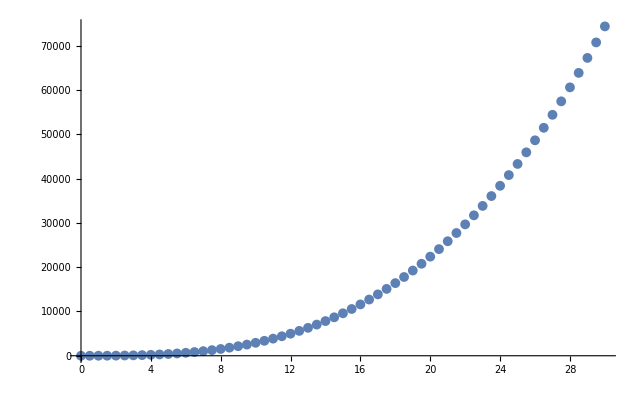

```mathematica
ListPlot[AK00]
```

```mathematica
fit=NonlinearModelFit[AK00[[2;;]],a+ b k + c k^2 + d k^3+e  k^4,{a,b,c,d,e},k]
```

FittedModel[0.768126-1.02598 k+2.70575 k^2+2.66501 k^3+0.0000240571 k^4]

It is clear the best fit is from the cubic polynomial without the k^4 term that is numerous orders of magnitude smaller than the others.

```mathematica
fit=NonlinearModelFit[AK00[[2;;]],a+ b k + c k^2 + d k^3,{a,b,c,d},k]
```

FittedModel[0.440584-0.826032 k+2.67682 k^2+2.66648 k^3]

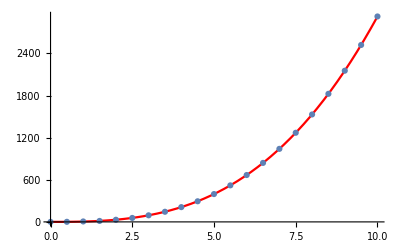

```mathematica
Show[Plot[Normal@fit,{k,0,10},PlotStyle->Red],ListPlot[AK00]]
```

```mathematica
fit["BestFitParameters"]
```

{a→0.440584,b→-0.826032,c→2.67682,d→2.66648}

```mathematica
fit["ParameterErrors"]
```

{0.125568,0.0353603,0.00268199,0.0000578309}

# Base divergence dim (2j+1)^2

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/src

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/BF/cutoff_30.0/heptapod_dim_2.csv";
```

```mathematica
{rAK00}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AK00} = Table[{k,#[[2k+1]]},{k,0,30,1/2}]&/@{rAK00};
```

### K=30 ib=0

We look at intertwiners ib1 = 0 ib2 = 0

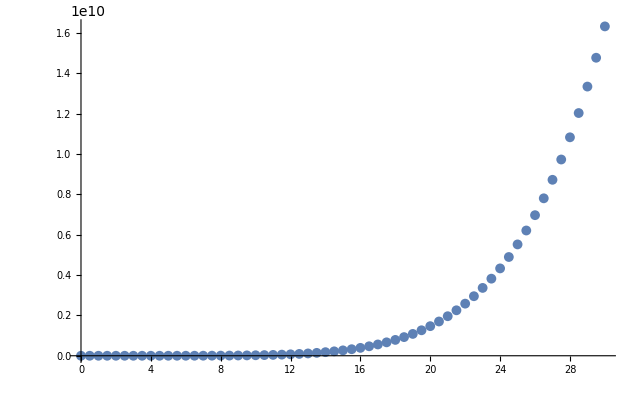

```mathematica
ListPlot[AK00]
```

```mathematica
fit=NonlinearModelFit[AK00[[2;;]],a+ b k + c k^2 + d k^3+e  k^4+f  k^5+g  k^6 + h k^7,{a,b,c,d,e,f,g,h},k]
```

FittedModel[108.502-68.354 k+16.1924 k^2-18.0202 k^3-2.53291 k^4+31.995 k^5+21.3334 k^6-7.79163×10^-7 k^7]

It is clear the best fit is from the cubic polynomial without the k^7 term that is numerous orders of magnitude smaller than the others.

```mathematica
fit=NonlinearModelFit[AK00[[2;;]],a+ b k + c k^2 + d k^3+e  k^4+f  k^5+g  k^6,{a,b,c,d,e,f,g,h},k]
```

FittedModel[100.728-56.7049 k+11.3864 k^2-17.1725 k^3-2.60812 k^4+31.9986 k^5+21.3333 k^6]

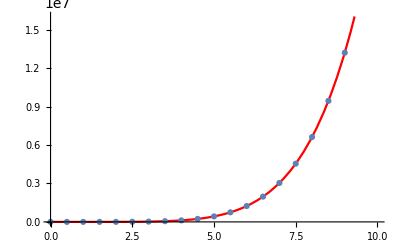

```mathematica
Show[Plot[Normal@fit,{k,0,10},PlotStyle->Red],ListPlot[AK00]]
```

```mathematica
fit["BestFitParameters"]
```

{a→0.440584,b→-0.826032,c→2.67682,d→2.66648}

```mathematica
fit["ParameterErrors"]
```

{0.125568,0.0353603,0.00268199,0.0000578309}

# Divergence boundary spins = 1/2

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/src

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/BF/cutoff_30.0/heptapod_bs05_prop.csv";
```

```mathematica
{rAK00,rAK01,rAK11}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AK00,AK01,AK11} = Table[{k,#[[2k+1]]},{k,0,30,1/2}]&/@{rAK00,rAK01,rAK11};
```

## Is K = 10 enough?

### K=10 ib=0

We look at intertwiners ib1 = 0 ib2 = 0

```mathematica
AK00cut10= AK00[[;;21]];
```

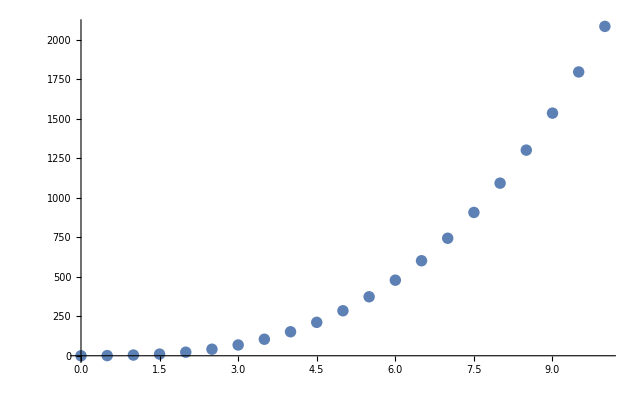

```mathematica
ListPlot[AK00cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK00cut10[[2;;]],b k^a+c k^(a-1) +d ,{a,b,c,d},k]
```

FittedModel[0.186547+1.74932 k^1.98583+1.97912 k^2.98583]

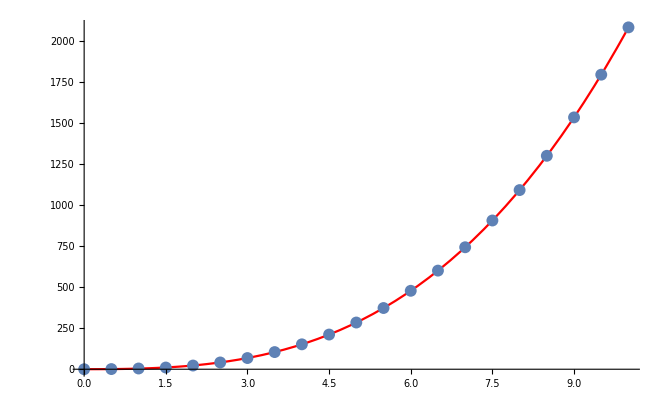

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK00cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.98583,b→1.97912,c→1.74932,d→0.186547}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.00373098,0.0237439,0.054642,0.125883}

### K=30 ib=0

Does the result change if we look at K up to 30?

```mathematica
fit30=NonlinearModelFit[AK00[[2;;]],b k^a+c k^(a-1) +d ,{a,b,c,d},k]
```

FittedModel[-0.412792+1.97282 k^1.99926+1.89191 k^2.99926]

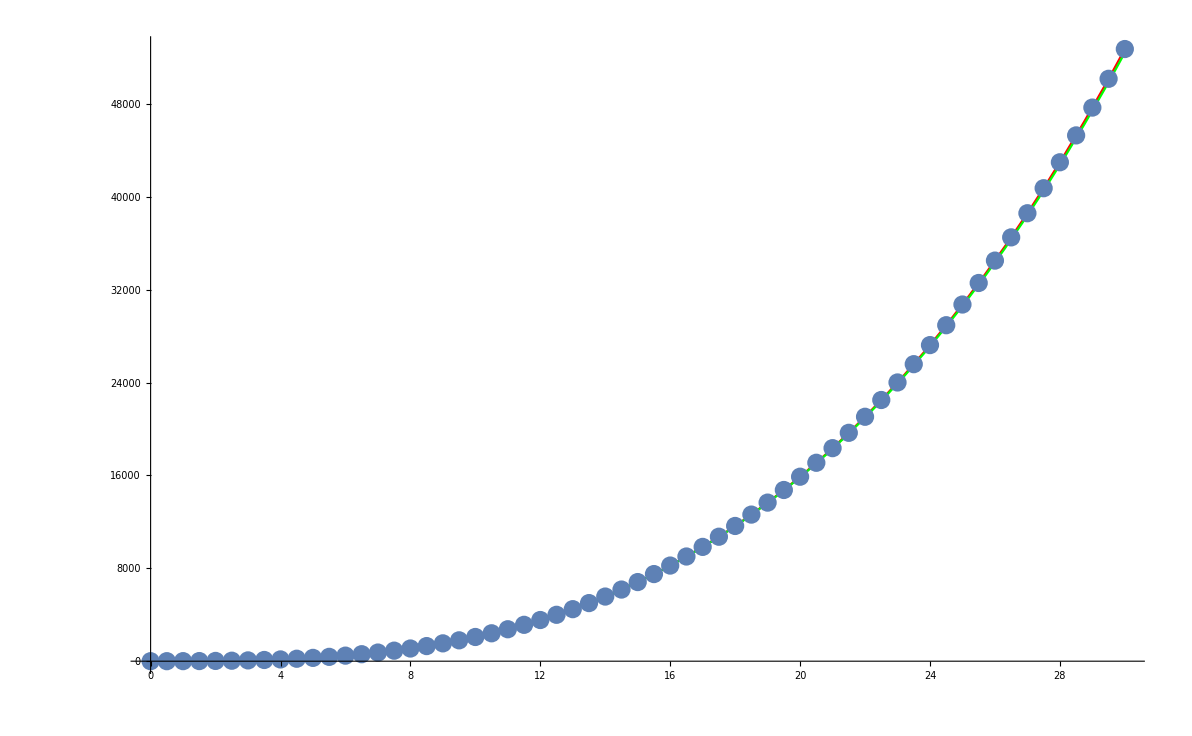

```mathematica
Show[Plot[{Normal@fit30,Normal@fitcutoff10},{k,0,30},PlotStyle->{Red,Green}],ListPlot[AK00]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.98583,b→1.97912,c→1.74932,d→0.186547}

```mathematica
fit30["BestFitParameters"]
```

{a→2.99926,b→1.89191,c→1.97282,d→-0.412792}

```mathematica
fit30["ParameterErrors"]
```

{0.0000752717,0.000602485,0.00319314,0.0678985}

## Is the result stable for different bdry?

### K=10 ib=1

We look at intertwiners ib1 = 1 ib2 = 1

```mathematica
AK11cut10= AK11[[;;21]];
```

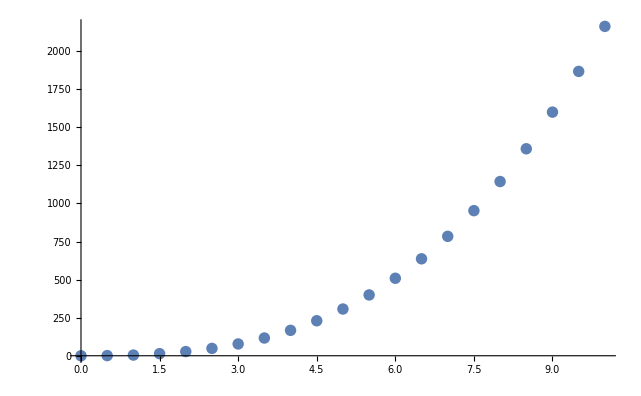

```mathematica
ListPlot[AK11cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK11cut10[[2;;]],b k^a+c k^(a-1)+e k +d ,{a,b,c,d,e},k]
```

FittedModel[-0.910141+1.55285 k+2.42487 k^1.99149+1.94753 k^2.99149]

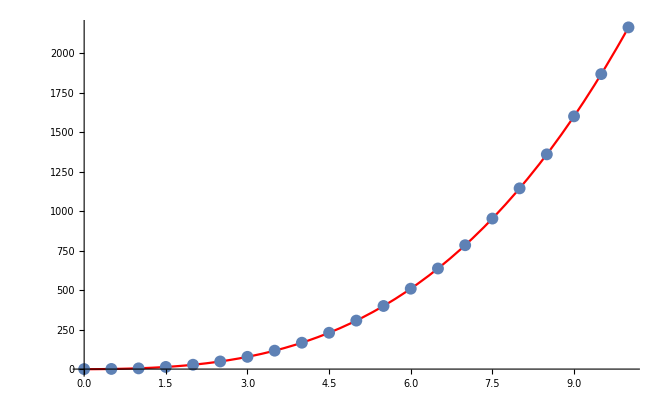

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK11cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.99149,b→1.94753,c→2.42487,d→-0.910141,e→1.55285}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.00888299,0.061021,0.199877,0.283156,0.390183}

## Are different intertwiners orthogonal? Nope

We look at intertwiners ib1 = 0 ib2 = 1

```mathematica
AK01cut10= AK01[[;;21]];
```

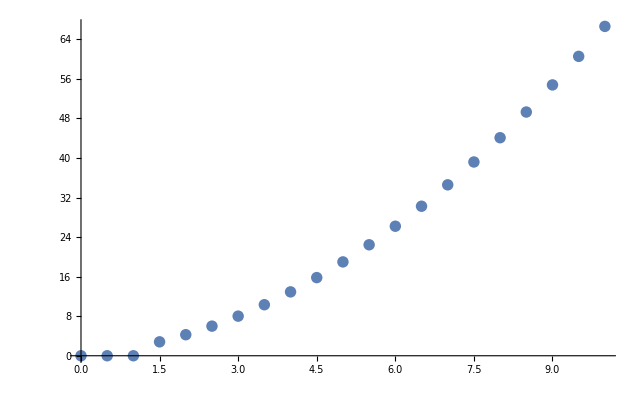

```mathematica
ListPlot[AK01cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK01cut10[[4;;]],b k^a+c k^(a-1)+d ,{a,b,c,d},k]
```

FittedModel[0.216506+0.866025 k^1.+0.57735 k^2.]

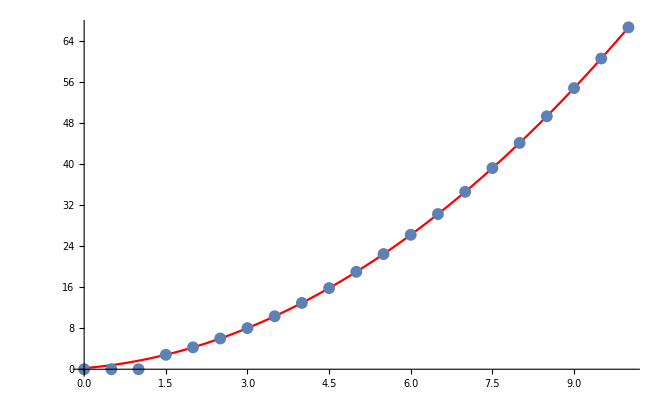

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK01cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.,b→0.57735,c→0.866025,d→0.216506}

```mathematica
fitcutoff10["ParameterErrors"]
```

{1.86025×10^-14,3.59545×10^-14,8.57121×10^-14,8.98401×10^-14}

# Divergence boundary spins = 1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/src

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/BF/cutoff_30.0/heptapod_bs10_prop.csv";
```

```mathematica
{rAK00,rAK01,rAK02,rAK11,rAK12,rAK22}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AK00,AK01,AK02,AK11,AK12,AK22}= Table[{k,#[[2k+1]]},{k,0,30,1/2}]&/@{rAK00,rAK01,rAK02,rAK11,rAK12,rAK22};
```

## Is K = 10 enough?

### K=10 ib=0

We look at intertwiners ib1 = 0 ib2 = 0

```mathematica
AK00cut10= AK00[[;;21]];
```

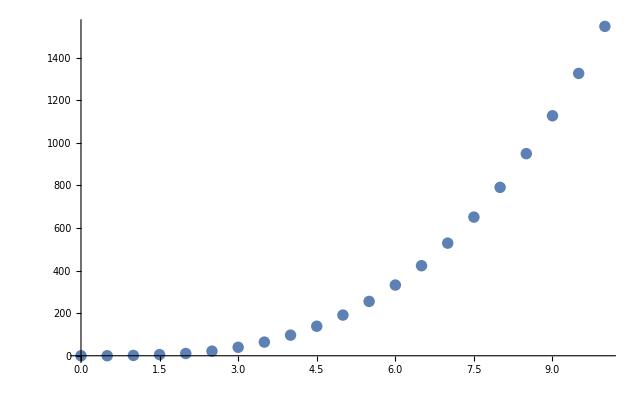

```mathematica
ListPlot[AK00cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK00cut10[[2;;]],b k^a+c k^(a-1) +d ,{a,b,c,d},k]
```

FittedModel[0.120057-0.660622 k^1.96158+1.75624 k^2.96158]

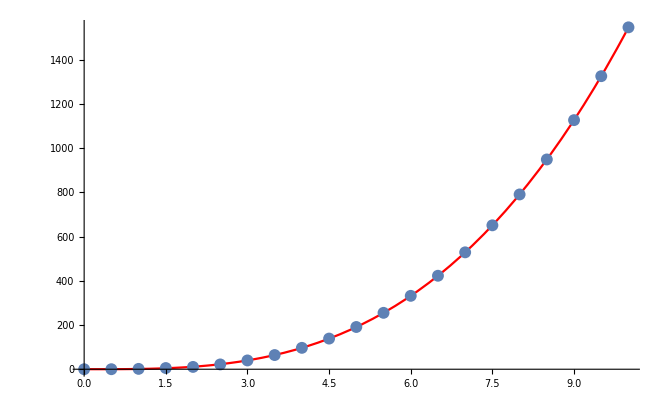

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK00cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.96158,b→1.75624,c→-0.660622,d→0.120057}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.00750086,0.0403706,0.116704,0.268975}

### K=30 ib=0

Does the result change if we look at K up to 30?

```mathematica
fit30=NonlinearModelFit[AK00[[2;;]],b k^a+c k^(a-1) +d ,{a,b,c,d},k]
```

FittedModel[-1.75197-0.0503609 k^1.99575+1.56961 k^2.99575]

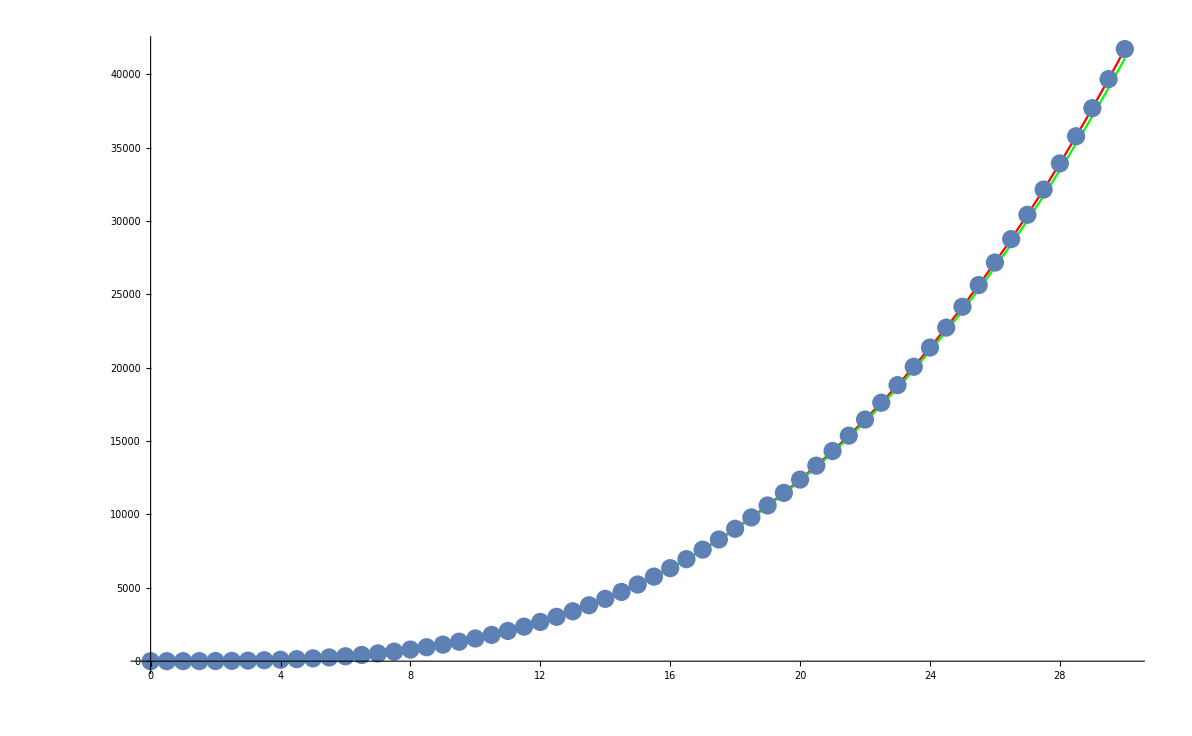

```mathematica
Show[Plot[{Normal@fit30,Normal@fitcutoff10},{k,0,30},PlotStyle->{Red,Green}],ListPlot[AK00]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.96158,b→1.75624,c→-0.660622,d→0.120057}

```mathematica
fit30["BestFitParameters"]
```

{a→2.99575,b→1.56961,c→-0.0503609,d→-1.75197}

```mathematica
fit30["ParameterErrors"]
```

{0.000262499,0.00172505,0.0102193,0.206785}

## Is the result stable for different bdry?

### K=10 ib=1

We look at intertwiners ib1 = 1 ib2 = 1

```mathematica
AK11cut10= AK11[[;;21]];
```

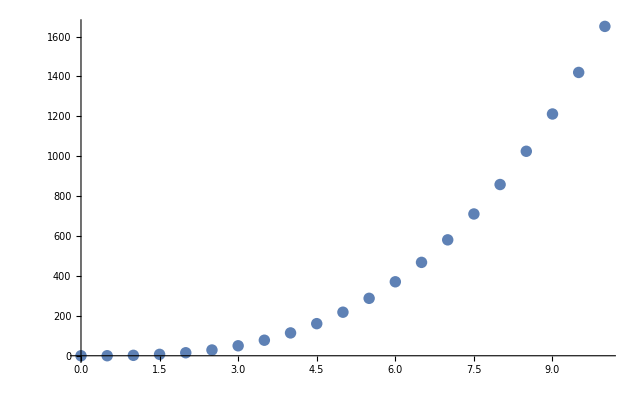

```mathematica
ListPlot[AK11cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK11cut10[[2;;]],b k^a+c k^(a-1)+e k +d ,{a,b,c,d,e},k]
```

FittedModel[0.52371-1.55965 k+1.53146 k^2.01623+1.45176 k^3.01623]

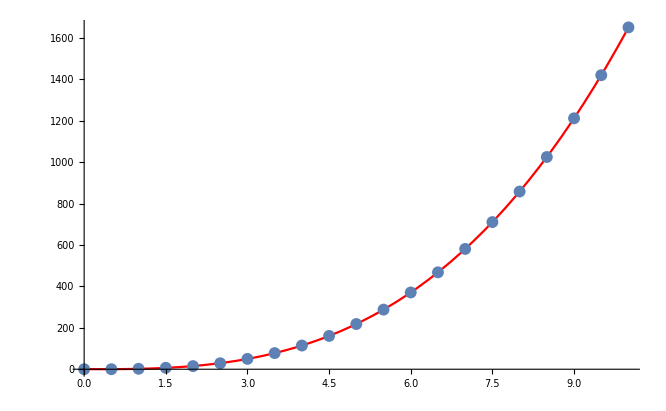

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK11cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→3.01623,b→1.45176,c→1.53146,d→0.52371,e→-1.55965}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.0144756,0.0737546,0.247736,0.364427,0.495933}

### K=10 ib=2

We look at intertwiners ib1 = 2 ib2 = 2

```mathematica
AK22cut10= AK22[[;;21]];
```

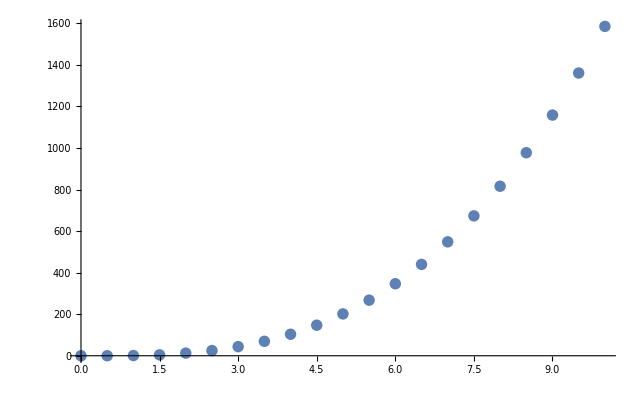

```mathematica
ListPlot[AK22cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK22cut10[[2;;]],b k^a+c k^(a-1)+e k +d ,{a,b,c,d,e},k]
```

FittedModel[0.296162-1.65661 k+0.940845 k^2.02122+1.43132 k^3.02122]

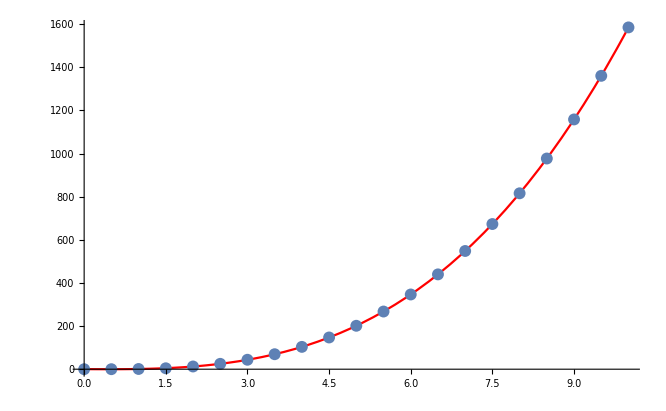

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK22cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→3.02122,b→1.43132,c→0.940845,d→0.296162,e→-1.65661}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.0115304,0.057432,0.206735,0.301163,0.415692}

## Are different intertwiners orthogonal? Nope

### K=10 ib=01

We look at intertwiners ib1 = 0 ib2 = 1

```mathematica
AK01cut10= AK01[[;;21]];
```

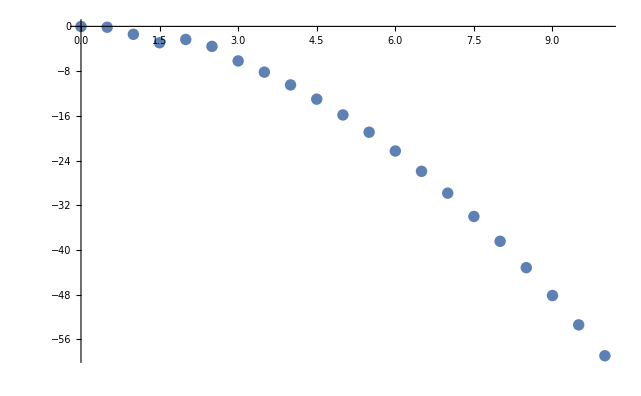

```mathematica
ListPlot[AK01cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK01cut10[[4;;]],b k^a+c k^(a-1)+d ,{a,b,c,d},k]
```

FittedModel[-3.34484+2.88926 k^0.712632-1.36211 k^1.71263]

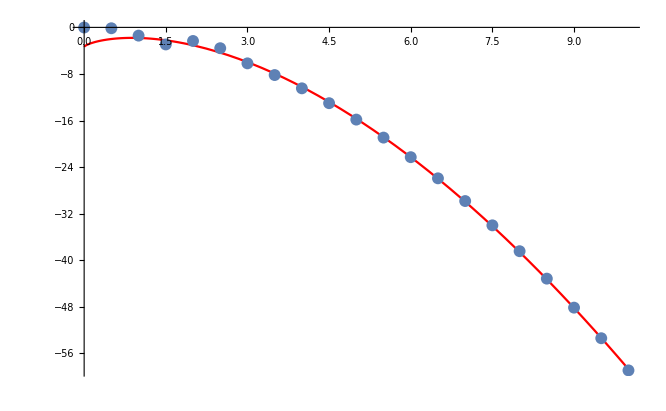

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK01cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→1.71263,b→-1.36211,c→2.88926,d→-3.34484}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.114578,0.479367,2.48839,2.55196}

### K=10 ib=02

We look at intertwiners ib1 = 0 ib2 = 1

```mathematica
AK02cut10= AK02[[;;21]];
```

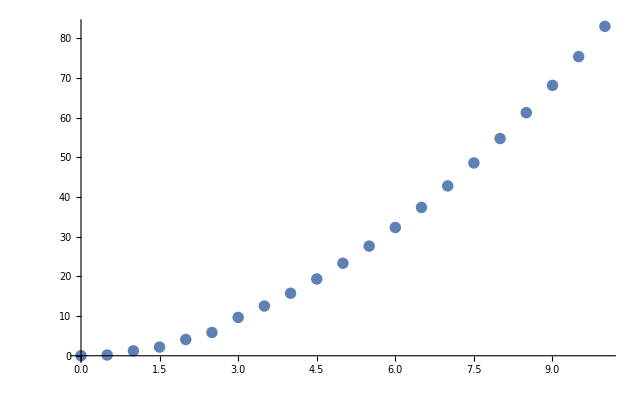

```mathematica
ListPlot[AK02cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK02cut10[[4;;]],b k^a+c k^(a-1)+d ,{a,b,c,d},k]
```

FittedModel[-1.73005+1.93457 k^1.31967+0.212413 k^2.31967]

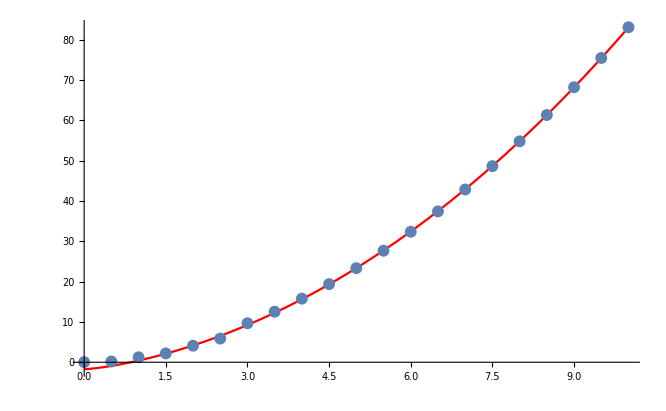

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK02cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.31967,b→0.212413,c→1.93457,d→-1.73005}

```mathematica
fitcutoff10["ParameterErrors"]
```

{1.2387,1.08646,0.826511,2.41344}

### K=10 ib=12

We look at intertwiners ib1 = 1 ib2 = 1

```mathematica
AK12cut10= AK12[[;;21]];
```

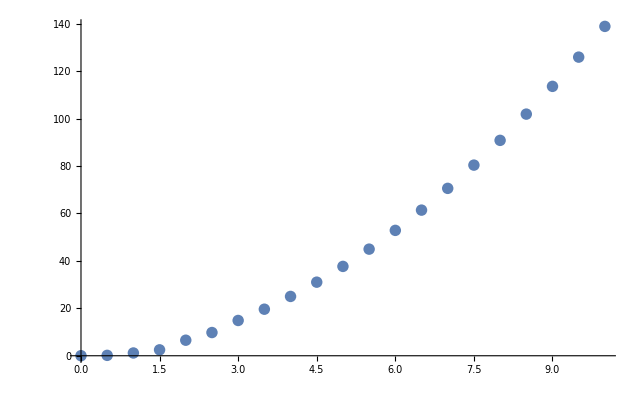

```mathematica
ListPlot[AK12cut10]
```

```mathematica
fitcutoff10=NonlinearModelFit[AK12cut10[[4;;]],b k^a+c k^(a-1)+d ,{a,b,c,d},k]
```

FittedModel[-3.18028+2.98575 k^1.29739+0.418057 k^2.29739]

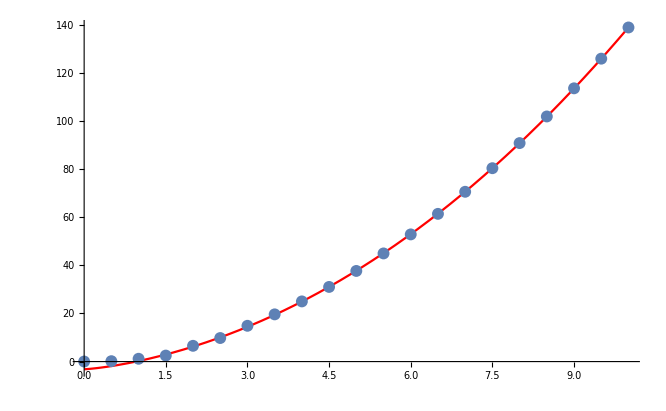

```mathematica
Show[Plot[Normal@fitcutoff10,{k,0,10},PlotStyle->Red],ListPlot[AK12cut10]]
```

```mathematica
fitcutoff10["BestFitParameters"]
```

{a→2.29739,b→0.418057,c→2.98575,d→-3.18028}

```mathematica
fitcutoff10["ParameterErrors"]
```

{0.383129,0.628059,0.0881858,0.7491}